```mathematica
params={g->9.8, c->1, m->1};
```

```mathematica
vel = NDSolveValue[{D[y[x], x]==g-c/m y[x]^2,y[0]==0}/.params,y, {x,0,1}];
pos = NDSolveValue[{D[v[t],{t,2}]==g-c/m v[t]^2,v[0]==0, v'[0]==0}/.params, v, {t,0,1}];
```

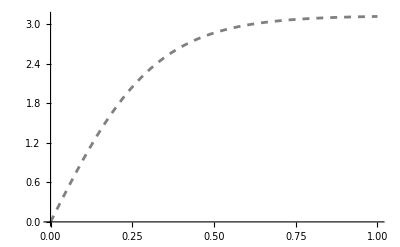

```mathematica
numSolPlot = Plot[vel[x], {x,0,1}, PlotStyle->{Dashed, Gray}]
```

```mathematica
vTerm=Sqrt[(m g)/c];
```

```mathematica
vAnalytic[t_]:=vTerm Tanh[(g t)/vTerm]
yAnalytic[t_]:=vTerm^2/g Log[Cosh[(g t)/vTerm]]
```

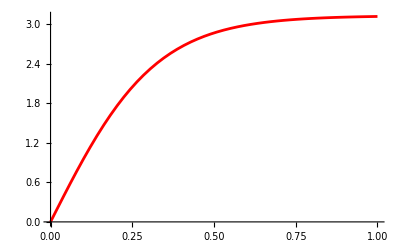

```mathematica
analSolPlot = Plot[vAnalytic[t]/.params,{t,0,1}, PlotStyle->Red]
```

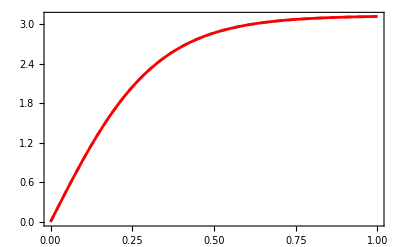

```mathematica
Show[numSolPlot, analSolPlot, Frame->True]
```

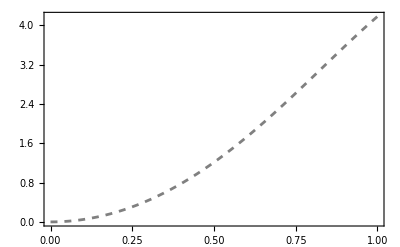

```mathematica
solNumPlot = Plot[pos[t],{t,0,1}, PlotStyle->{Dashed, Gray}, Frame->True]
```

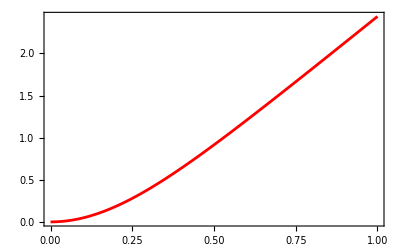

```mathematica
vAnalyticPlot = Plot[yAnalytic[t]/.params,{t,0,1}, PlotStyle->Red, Frame->True]
```

```mathematica
vAnalytic[t]/.params
```

3.1305 Tanh[3.1305 t]